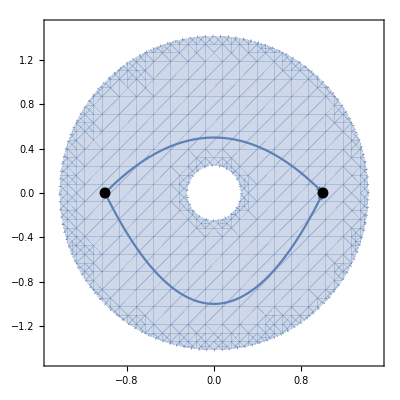

```mathematica
ApplyArrows[p_,spacing_]:=p/.Line[x_]:>{Arrowheads[spacing],Arrow[x]};
ParaPlot[f_]:=ApplyArrows[
ParametricPlot[{t,f},{t,-1,1}],
{0,.05,0,0,.05,0}
];
Show[
RegionPlot[1/16<x^2+y^2<2,{x,-1.5,1.5},{y,-1.5,1.5},BoundaryStyle->{Dotted,Thickness[0.005]}],
(* ParaPlot[Cos[t*Pi*3/2]/2+(1-t^2)/2], *)
ParaPlot[(1-t^2)/2],
ParaPlot[t^2-1],
Graphics[{Black,Disk[{1,0},0.05],Disk[{-1,0},0.05]}]
]
```

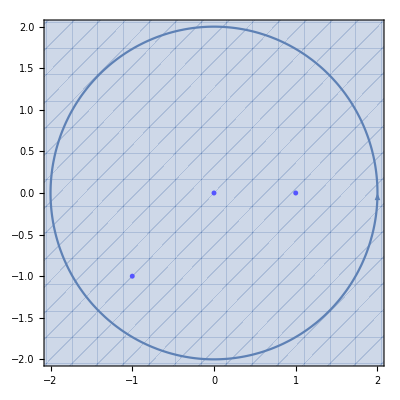

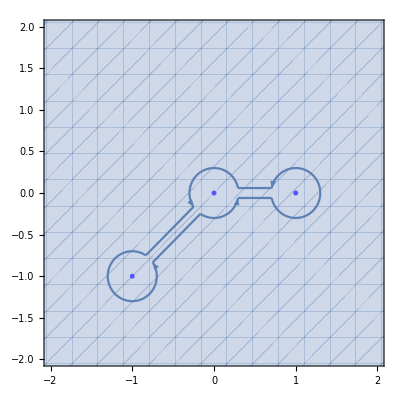

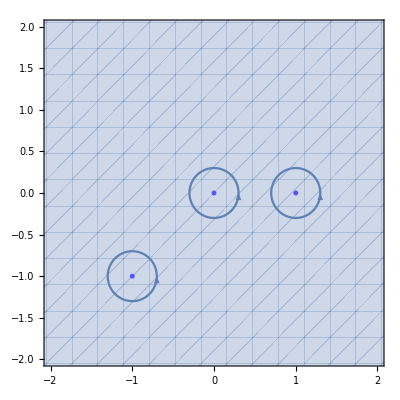

```mathematica
DrawContour[c_]:=Show[
RegionPlot[True,{x,-3,3},{y,-3,3}],
Graphics[{
Lighter[Blue],
Disk[{0,0},0.03],
Disk[{-1,-1},0.03],
Disk[{1,0},0.03],
}],
c,
PlotRange->{{-2,2},{-2,2}}
];
DrawContour[Show[
ApplyArrows[
ParametricPlot[{2*Cos[t],2*Sin[t]},{t,0,2Pi}],
{0,.05,0,.05,0,.05,0}
]
]]

eps=0.2;
LineBetween[x1_,y1_,x2_,y2_,phi_]:=ParametricPlot[
{
{
t*(0.3*Cos[phi+eps]+x1)+(1-t)*(0.3*Cos[phi-eps+Pi]+x2),
t*(0.3*Sin[phi+eps]+y1)+(1-t)*(0.3*Sin[phi-eps+Pi]+y2)
},
{
t*(0.3*Cos[phi-eps]+x1)+(1-t)*(0.3*Cos[phi+eps+Pi]+x2),
t*(0.3*Sin[phi-eps]+y1)+(1-t)*(0.3*Sin[phi+eps+Pi]+y2)
}
},
{t,0,1},
PlotStyle->ColorData[97,"ColorList"][[1]]
]
DrawContour[Show[
ApplyArrows[
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,eps,5/4*Pi-eps}],
{0,.05,0}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,5/4*Pi+eps,2Pi-eps}],
{0,.05,0}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t]+1,0.3Sin[t]},{t,Pi+eps,3Pi-eps}],
{0,.05,0}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t]-1,0.3Sin[t]-1},{t,Pi/4+eps,9/4Pi-eps}],
{0,.05,0}
],
LineBetween[0,0,1,0,0],
LineBetween[0,0,-1,-1,5/4Pi]
]]

DrawContour[Show[
ApplyArrows[
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,0,2Pi}],
{0,.05,0}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t]+1,0.3Sin[t]},{t,0,2Pi}],
{0,.05,0}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t]-1,0.3Sin[t]-1},{t,0,2Pi}],
{0,.05,0}
]
]]
```

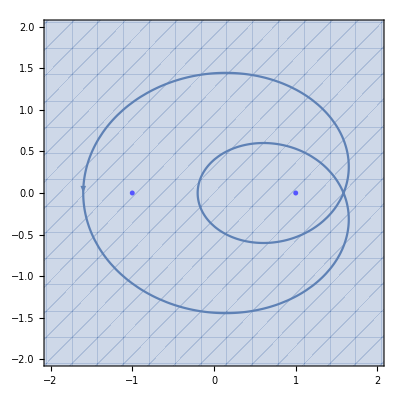

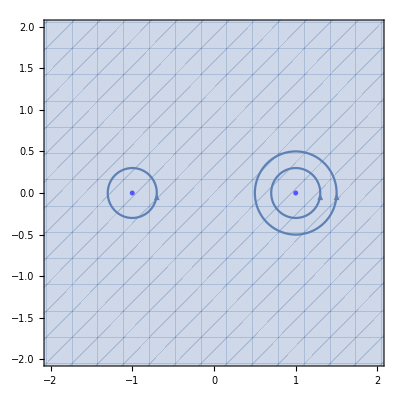

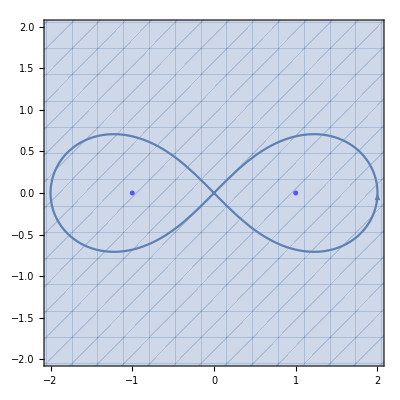

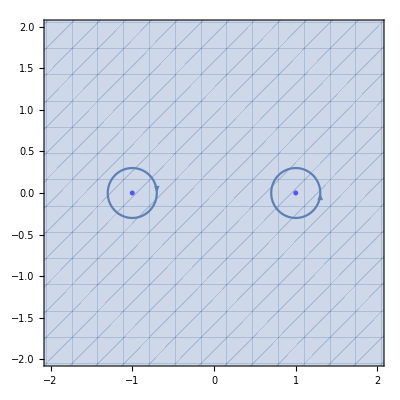

```mathematica
DrawContour2[c_]:=Show[
RegionPlot[True,{x,-3,3},{y,-3,3}],
Graphics[{
Lighter[Blue],
Disk[{1,0},0.03],
Disk[{-1,0},0.03],
}],
c,
PlotRange->{{-2,2},{-2,2}}
];
DrawContour2[Show[
ApplyArrows[
ParametricPlot[
{1.6-(0.7+2.5Cos[t])Cos[t],-(0.6+2Cos[t])Sin[t]},
{t,0,2Pi}
],
{0,0,0,.05,0,0,.05,0,0,0,.05}
]
]]
DrawContour2[Show[
ApplyArrows[
ParametricPlot[{0.3Cos[t]+1,0.3Sin[t]},{t,0,2Pi}],
{.05}
],
ApplyArrows[
ParametricPlot[{0.5Cos[t]+1,0.5Sin[t]},{t,0,2Pi}],
{.05}
],
ApplyArrows[
ParametricPlot[{0.3Cos[t]-1,0.3Sin[t]},{t,0,2Pi}],
{.05}
]
]]
DrawContour2[Show[
ApplyArrows[
ParametricPlot[
{(2Cos[t])/(1+Sin[t]^2),(2Cos[t]Sin[t])/(1+Sin[t]^2)},
{t,0,2Pi}
],
{0,.05,0,0,.05,0,.05,0}
]
]]
DrawContour2[Show[
ApplyArrows[
ParametricPlot[{0.3Cos[t]+1,0.3Sin[t]},{t,0,2Pi}],
{.05}
],
ApplyArrows[
ParametricPlot[{0.3Cos[-t]-1,-0.3Sin[t]},{t,0,2Pi}],
{.05}
]
]]
```